```mathematica
(*Question No 1(a)*)
```

```mathematica
f1[x_]:=(x^2+2x)/(x^2-1);
f2[x_]:=(x^2-1)/(x^4+1);
f3[x_]:=Tan[x];
f4[x_]:=Csc[x];
f5[x_]:=Exp[x+1]-2;
f6[x_]:=ArcSec[x];
f7[x_]:=1-2^x;
f8[x_]:=Log[2-x^2];
f9[x_]:=1-Abs[2-3x];
```

x<-1||-1<x<1||x>1

True

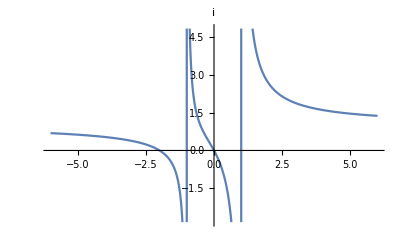

```mathematica
domain=FunctionDomain[f1[x],x]
range=FunctionRange[f1[x],x,y]
Plot[f1[x],{x,-6,6},Exclusions->domain,PlotLabel->"i"]
```

True

-1≤y≤(√2)/(1+(1+√2)^2)

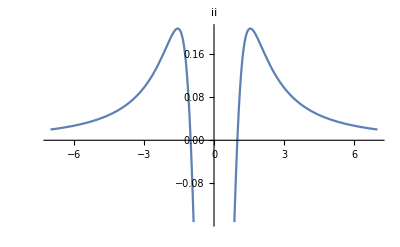

```mathematica
domain=FunctionDomain[f2[x],x]
range=FunctionRange[f2[x],x,y]
Plot[f2[x],{x,-7,7},Exclusions->domain,PlotLabel->"ii"]
```

```mathematica
(*iii*)
```

1/2+x/π∉ℤ

True

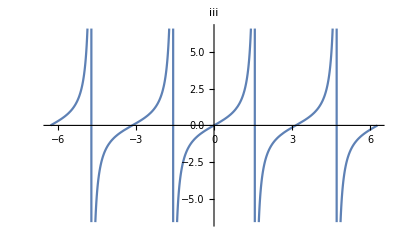

```mathematica
domain=FunctionDomain[f3[x],x]
range=FunctionRange[f3[x],x,y]
Plot[f3[x],{x,-2π,2π},PlotLabel->"iii"]
```

```mathematica
(*iv*)
```

x/π∉ℤ

y≤-1||y≥1

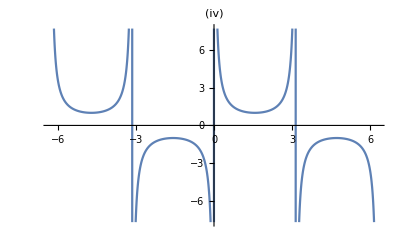

```mathematica
domain=FunctionDomain[f4[x],x]
range=FunctionRange[f4[x],x,y]
Plot[f4[x],{x,-2π,2π},PlotLabel->"(iv)"]
```

```mathematica
(*v*)
```

True

y>-2

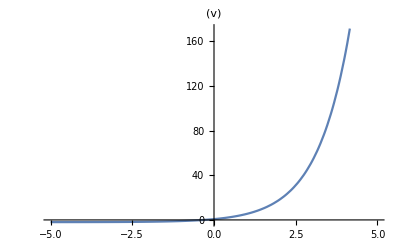

```mathematica
domain=FunctionDomain[f5[x],x]
range=FunctionRange[f5[x],x,y]
Plot[f5[x],{x,-5,5},PlotLabel->"(v)"]
```

```mathematica
(*vi*)
```

x≤-1||x≥1

0≤y<π/2||π/2<y≤π

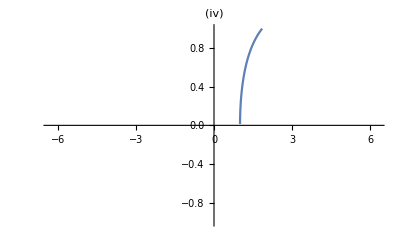

```mathematica
domain=FunctionDomain[f6[x],x]
range=FunctionRange[f6[x],x,y]
Plot[f6[x],{x,-2π,2π},PlotLabel->"(iv)",PlotRange->{-1,1}]
```

```mathematica
(*vii*)
```

True

y<1

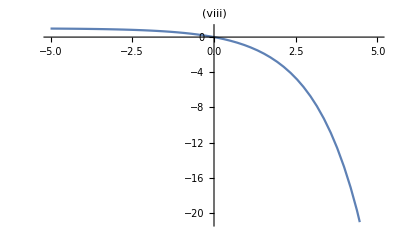

```mathematica
domain=FunctionDomain[f7[x],x]
range=FunctionRange[f7[x],x,y]
Plot[f7[x],{x,-5,5},PlotLabel->"(viii)"]
```

```mathematica
(*ix*)
```

True

y≤1

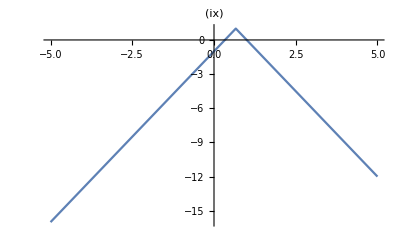

```mathematica
domain=FunctionDomain[f9[x],x]
range=FunctionRange[f9[x],x,y]
Plot[f9[x],{x,-5,5},PlotLabel->"(ix)"]
```

```mathematica
(*Question No 1(b)*)
```

```mathematica
Exit
```

Question No 1(b)

```mathematica
(*i*)
```

```mathematica
f1[x_]:=-1/(Sqrt[2x-3]);
```

x>3/2

y<0

(1+3 #1^2)/(2 #1^2)&

(1+3 x^2)/(2 x^2)

x<0||x>0

y>3/2

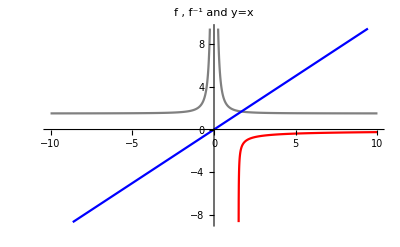

```mathematica
domain=FunctionDomain[f1[x],x]
range=FunctionRange[f1[x],x,y]
invf=InverseFunction[f1]
invf[x]
invdomain=FunctionDomain[invf[x],x]
invfrange=FunctionRange[invf[x],x,y]
Plot[{f1[x],invf[x],x},{x,-10,10},PlotStyle->{Red,Gray,Blue},PlotLabel->"f , f^-1 and y=x"]
```

```mathematica
(*ii*)
```

x≤1/3

y≤2

1/3 (-3+4 #1-#1^2)&

1/3 (-3+4 x-x^2)

True

y≤1/3

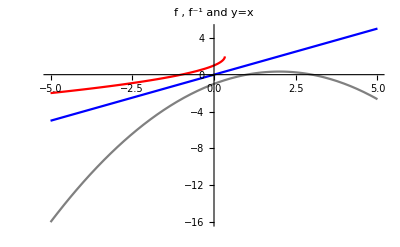

```mathematica
f3[x_]:=2-Sqrt[1-3x];
domain=FunctionDomain[f3[x],x]
range=FunctionRange[f3[x],x,y]
invf=InverseFunction[f3]
invf[x]
invdomain=FunctionDomain[invf[x],x]
invfrange=FunctionRange[invf[x],x,y]
Plot[{f3[x],invf[x],x},{x,-5,5},PlotStyle->{Red,Gray,Blue},PlotRange->All,PlotLabel->"f , f^-1 and y=x"]
```

```mathematica
Exit
```

Question No 1(c)

```mathematica
f[x_]:=x^2+3;
g[x_]:=Sqrt[x];
fog=f[g[x]]
gof=g[f[x]]
soln=fog==gof
```

3+x

√(3+x^2)

3+x==√(3+x^2)

Question No 1(d)

```mathematica
Exit
```

```mathematica
f[t_]:=0.0729*Exp[0.45t];
(*i*)
i=2031-2017;
f[i]
(*ii*)
ii=Solve[f[t]==19,t]
year=2017+ii//N
```

39.6993

{{t→12.3625}}

{{2017.+(t→12.3625)}}

```mathematica
Exit
```

```mathematica
(*Question No 2*)
```

Question No 2(a)

```mathematica
f[x_]:=Piecewise[{
{1/(x+2),x<-2},
{x^2-5,-2<x<=3},
{Sqrt[x+13],x>3}
}];
(*i*)
limit1l=Limit[f[x],x->-2,Direction->"FromAbove"]
limit1r=Limit[f[x],x->-2,Direction->"FromBelow"]
limit1=If[limit1l==limit1r,limit1l,"limit does not exit"]
```

-1

-∞

limit does not exit

```mathematica
(*ii*)
```

```mathematica
limit2l=Limit[f[x],x->0,Direction->"FromAbove"]
limit2r=Limit[f[x],x->0,Direction->"FromBelow"]
limi21=If[limit2l==limit2r,limit2l,"limit does not exit"]
```

-5

-5

-5

```mathematica
(*iii*)
```

```mathematica
limit3l=Limit[f[x],x->3,Direction->"FromAbove"]
limit3r=Limit[f[x],x->3,Direction->"FromBelow"]
limit3=If[limit3l==limit3r,limit3l,"limit does not exit"]
```

4

4

4

```mathematica
Exit
```

Question no 2(b)

```mathematica
v[t_]:=190(1-Exp[-0.168t]);
```

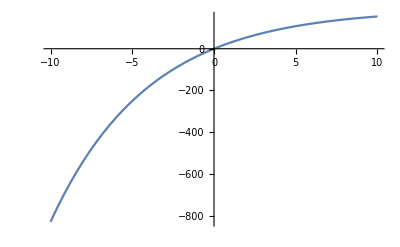

```mathematica
(*i*)
Plot[v[t],{t,-10,10}]
```

```mathematica
(*ii*)
slop=D[v[t],t]
```

31.92 ⅇ^(-0.168 t)

Question NO 3(a)

```mathematica
(*i*)
```

{{x→-3},{x→-2},{x→2}}

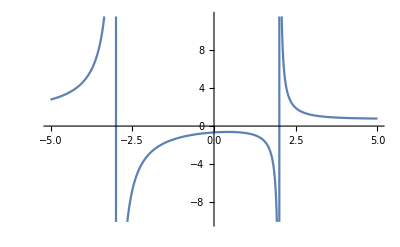

```mathematica
f[x_]:=(x^3+8)/(x^3+3x^2-4x-12);
Solve[x^3+3x^2-4x-12==0,x]
Plot[f[x],{x,-5,5}]
```

```mathematica
Exit
```

```mathematica
(*ii*)
```

{{x→0}}

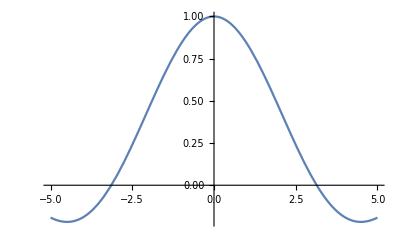

```mathematica
f[x_]:=Piecewise[{
{Sin[x]/x,x!=0},
{0.5,x=0}
}];
Solve[x==0,x]
Plot[f[x],{x,-5,5}]
```

```mathematica
Exit
```

```mathematica
(*iii*)
```

```mathematica
f[x_]:=Piecewise[{
{0,x<-1},
{}
}]
```